```mathematica
Manipulate[
f=Function[x,x^2];
f1=Plot[{f[x],f[1]+e,f[1]-e,f[1]},{x,0,1.5},PlotRange->All,Filling->{2->{3}},AspectRatio->Automatic,AxesLabel->None,Ticks->None,PlotStyle->{{},Dashed,Dashed,Dashed}];
f2=ParametricPlot[{1,y},{x,0,1},{y,0,1},PlotStyle->Dashed];
d=0.9*Min[Sqrt[f[1]+e]-1,1-Sqrt[f[1]-e]];
f3=ParametricPlot[{1+d,y},{x,0,1},{y,0,f[1+d]},PlotStyle->Dashed];
f4=ParametricPlot[{1-d,y},{x,0,1},{y,0,f[1-d]},PlotStyle->Dashed];
f5=Plot[f[x],{x,1-d,1+d},PlotStyle->{Red,Thick}];
Show[f1,f2,f3,f4,f5],
{e,0.1,0.5}]
```

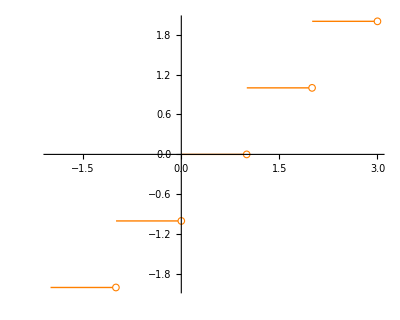

```mathematica
f11=Plot[Round[x-0.5],{x,-2,3},AspectRatio->Automatic,PlotStyle->{Orange,Thick}];
f12=Graphics[
{
{White,EdgeForm[Orange],Disk[{1,0},0.05]},
{White,EdgeForm[Orange],Disk[{2,1},0.05]},
{White,EdgeForm[Orange],Disk[{3,2},0.05]},
{White,EdgeForm[Orange],Disk[{0,-1},0.05]},
{White,EdgeForm[Orange],Disk[{-1,-2},0.05]}
}
];
Show[f11,f12]
```

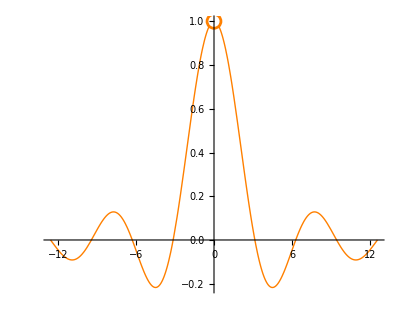

```mathematica
f21=Plot[Sin[x]/x,{x,-4Pi,4Pi},AspectRatio->0.8,PlotStyle->{Orange,Thick}];
f22=Graphics[
{
{PointSize[0.03],Orange,Point[{0,1}]}
}
];
f23=Graphics[
{
{PointSize[0.02],White,Point[{0,1}]}
}
];
Show[f21,f22,f23]
```

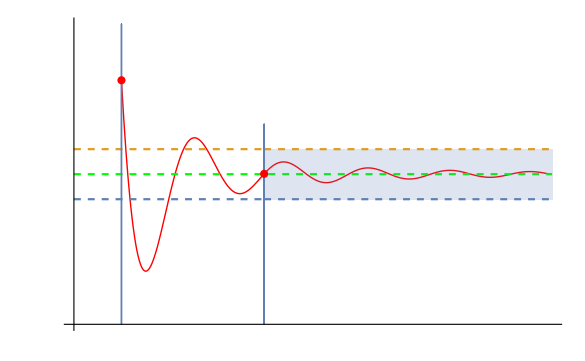

```mathematica
gf=Function[x,3Sin[x^1.1]/(x^2)+0.3];
f31=Plot[gf[x],{x,2.5,8Pi},AxesOrigin->{0,0},Ticks->None,PlotRange->All,PlotStyle->{Red,Thick}];
f32=Plot[{0.25,0.35},{x,0,10},PlotStyle->Dashed];
f321=Plot[0.3,{x,0,8Pi},PlotStyle->{Dashed,Green}];
f322=Plot[{0.25,0.35},{x,10,8Pi},PlotStyle->Dashed,Filling->{1->{2}}];
f33=ParametricPlot[{10,y},{x,0,1},{y,0,0.4}];
f34=ParametricPlot[{2.5,y},{x,0,1},{y,0,0.6}];
f35=Graphics[{
{PointSize[0.01],Red,Point[{2.5,gf[2.5]}]},
{PointSize[0.01],Red,Point[{10,gf[10]}]}
}];
Show[f31,f32,f321,f322,f33,f34,f35]
```

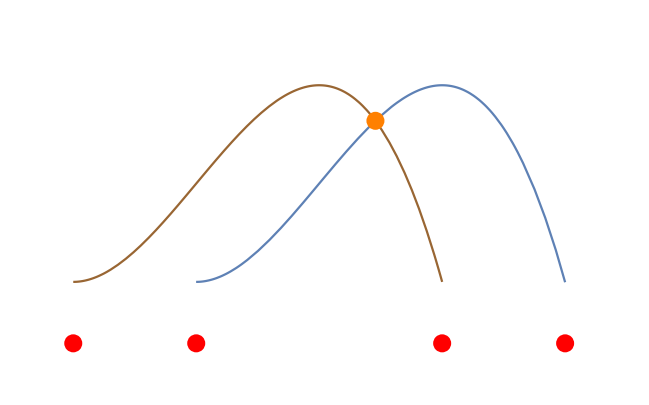

```mathematica
fff=Function[x,-x^2(x-3)/2.5+0.5];
fdd=(3+Sqrt[33])/6;
f411=Plot[{fff[x]},{x,-1.2,3.2},RegionFunction->Function[x,x>0&&x<3],
PlotRange->{-0.2,2.5},AspectRatio->Automatic,Axes->False,Ticks->{{-1,0,1, 2,3}, None}];
f412=Plot[{fff[x+1]},{x,-1,2},PlotStyle->Brown];
f42=Graphics[{
{PointSize[0.02],Red,Point[{{-1,0},{0,0},{2,0},{3,0}}]}
}];
f43=Graphics[{
{PointSize[0.02],Orange,Point[{fdd,fff[fdd]}]}
}];
(*f45=ParametricPlot[{fdd,y},{x,0,1},{y,0,fff[fdd]},PlotStyle->Directive[Gray]];*)
Show[f411,f412,f42,f43]
```

```mathematica
Solve[fff[x]==fff[x+1],x]
```

{{x→1/6 (3-√33)},{x→1/6 (3+√33)}}

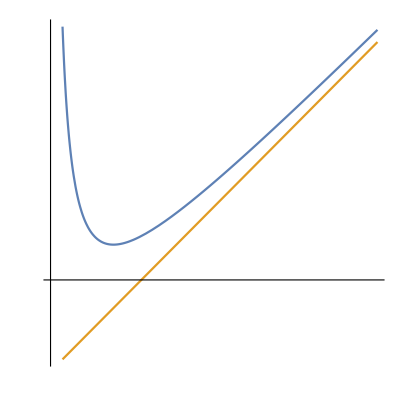

```mathematica
Plot[{3x+1/x-2.5,3x-2.5},{x,0.11,3},AxesOrigin->{0,0},AspectRatio->1,Ticks->None]
```

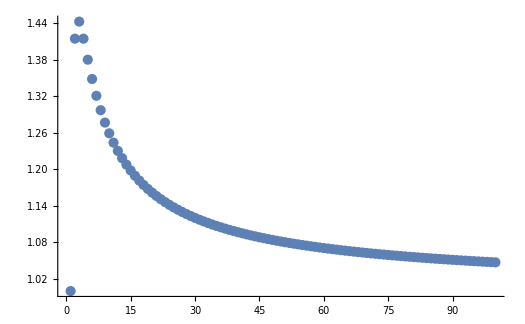

```mathematica
ListPlot[Table[n^(1/n),{n,100}]]
```

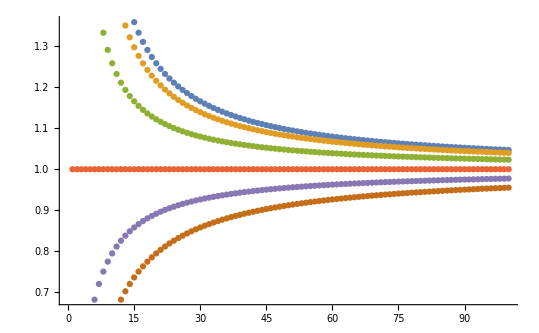

```mathematica
ListPlot[{
Table[100^(1/n),{n,100}],
Table[50^(1/n),{n,100}],
Table[10^(1/n),{n,100}],
Table[1^(1/n),{n,100}],
Table[0.1^(1/n),{n,100}],
Table[0.01^(1/n),{n,100}]
}]
```

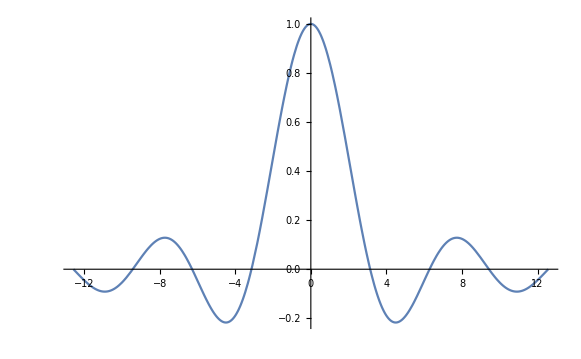

```mathematica
Plot[Sin[x]/x,{x,-4Pi,4Pi}]
```

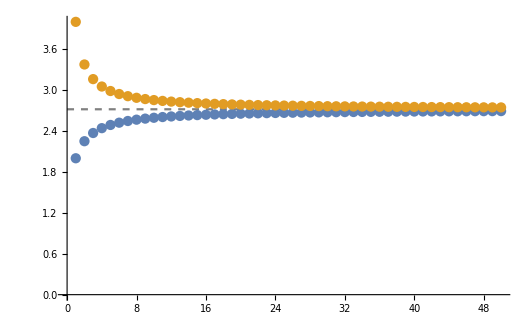

```mathematica
steps=50;
aEs=ListPlot[{
Table[(1+1/n)^n,{n,steps}],
Table[(1+1/n)^(n+1),{n,steps}]
},PlotRange-> All
];
horiLine=Plot[E,{x,0,steps},PlotStyle->{Dashed,Gray}];
Show[aEs,horiLine]
```

```mathematica
PolarPlot[(Cos[t-Pi/4])^9+2+1.1Sin[t+0.4Pi]^2,{t,0,2Pi},Axes->False,PlotStyle->Thick]
```

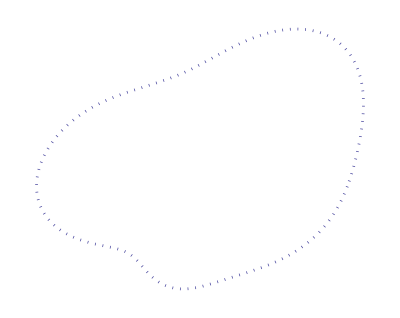

```mathematica
PolarPlot[Cos[t-π/4]^9+2+1.1 Sin[t+0.4 π]^2,{t,0,2 π},PlotStyle->Directive[Hue[0.67,0.6,0.6],Opacity[1.],AbsoluteThickness[2.],Dotted],Axes->False]
```

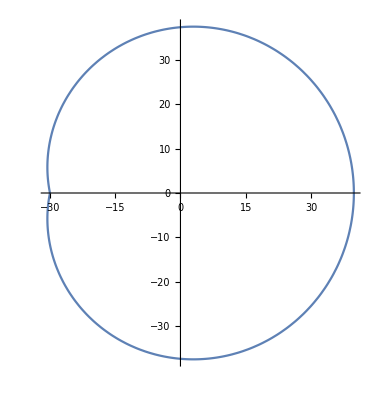

```mathematica
PolarPlot[(t-2Pi)t-30,{t,0,2Pi}]
```

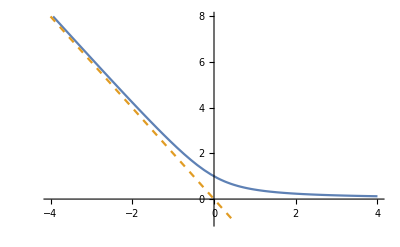

```mathematica
Plot[{Sqrt[x^2+1]-x,-2x},{x,-4,4},PlotStyle->{{},Dashed},PlotRange->{-1,8}]
```

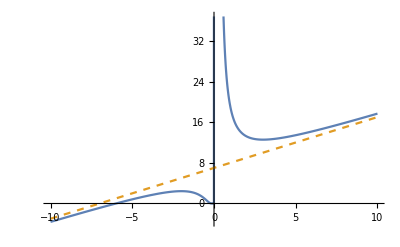

```mathematica
Plot[{(x+6)E^(1/x),x+7},{x,-10,10},PlotStyle->{{},Dashed}]
```

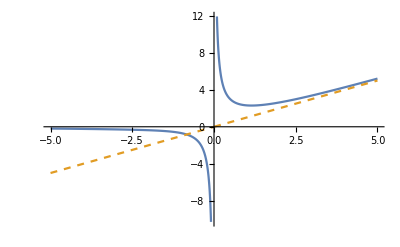

```mathematica
Plot[{1/x+Log[1+E^x],x},{x,-5,5},PlotStyle->{{},Dashed},Exclusions->{0}]
```

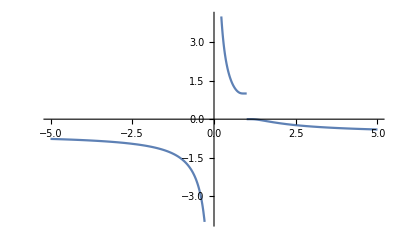

```mathematica
Plot[1/(1-E^{x/(x-1)}),{x,-5,5},PlotRange->{-4,4},Exclusions->{0,1}]
```

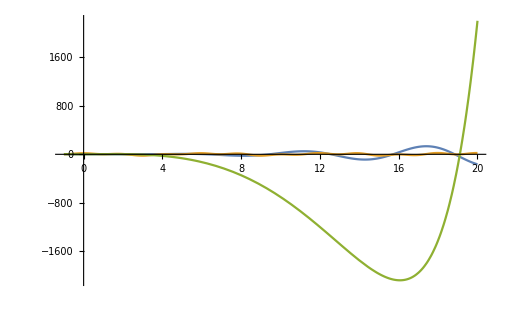

```mathematica
Plot[{-(0.5x^2-x)Sin[x],12Sin[9-2Cos[x]]+10Cos[Pi*x],(1.58)^x-x^3+2x^2},{x,-1,20},PlotRange->All]
```

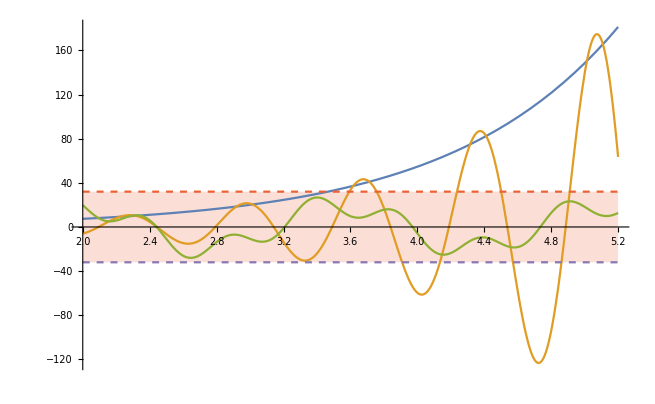

```mathematica
Plot[{E^x,1.1E^x*Sin[9x],20Sin[4x]-10Sin[4Pi*x],32,-32},{x,2,5.2},PlotStyle-> {{},{},{},Dashed,Dashed},PlotRange->All,Filling->{4->{5}}]
```

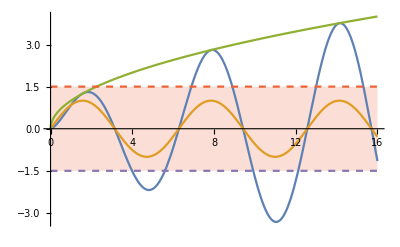

```mathematica
Plot[{Sqrt[x]*Sin[x],Sin[x],Sqrt[x],1.5,-1.5},{x,0,16},PlotStyle-> {{},{},{},Dashed,Dashed},PlotRange->All,Filling->{4->{5}}]
```

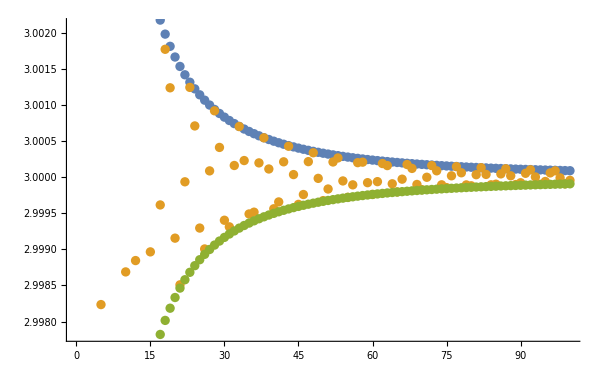

```mathematica
ListPlot[{Table[1/(n^2+10n)+3,{n,100}],Table[Sin[5n]/(n^2+10n)+3,{n,100}],
Table[-1/(n^2+10n)+3,{n,100}]}]
```

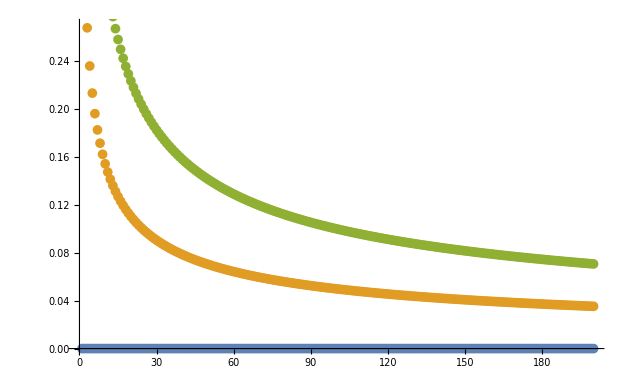

```mathematica
ListPlot[{Table[0,{n,200}],Table[Sqrt[n+1]-Sqrt[n],{n,200}],
Table[1/Sqrt[n],{n,200}]}]
```

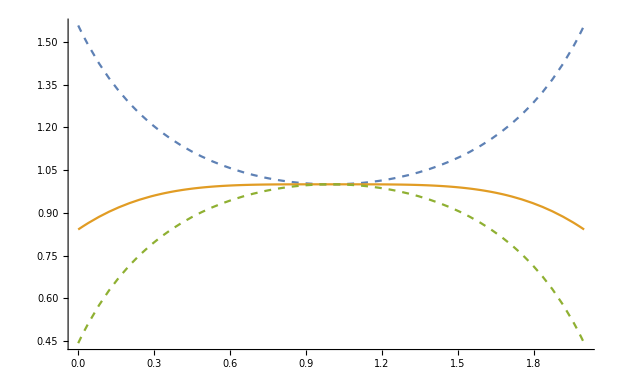

```mathematica
Plot[{Tan[x-1]/(x-1),(Sin[(x-1)^2])/(x-1)^2,-Tan[x-1]/(x-1)+2},{x,0,2},PlotStyle->{Dashed,{},Dashed}]
```

```mathematica
Plot[{},{x,0,2}]
```

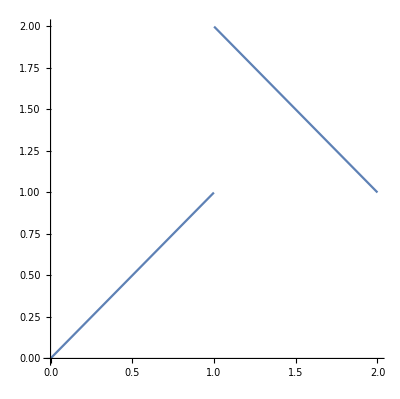

```mathematica
Plot[Piecewise[{{x,x<1},{3-x,x>1}}],{x,0,2},AspectRatio->Automatic]
```

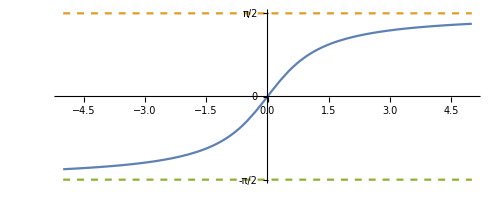

```mathematica
Plot[{ArcTan[x],Pi/2,-Pi/2},{x,-5,5},AspectRatio->Automatic,PlotStyle->{{},Dashed,Dashed},Ticks->{Automatic,{Pi/2,0,-Pi/2}}]
```

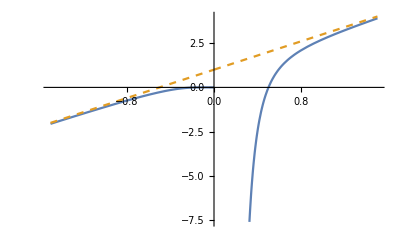

```mathematica
Plot[{(2x-1)E^(1/x),2x+1},{x,-1.5,1.5},Exclusions->{0},PlotStyle->{{},Dashed}]
```

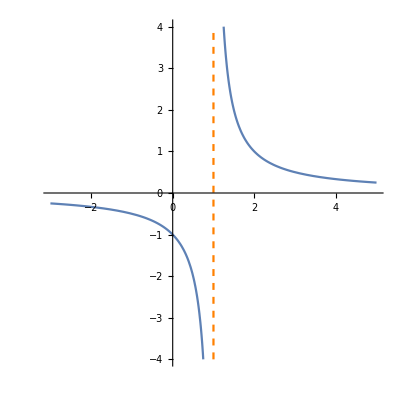

```mathematica
d11=Plot[{1/(x-1)},{x,-3,5},Exclusions->{1},Axes->True,Ticks->Automatic,PlotRange->{-4,4},AspectRatio->Automatic];
d12=ContourPlot[x==1,{x,-3,5},{y,-4,4},ContourStyle->{Orange,Dashed}];
Show[d11,d12]
```

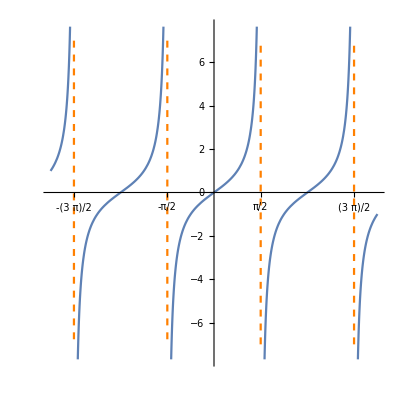

```mathematica
e11=Plot[Tan[x],{x,-5.5,5.5},Exclusions->{-Pi/2,Pi/2,3/2Pi,-3/2Pi},AspectRatio->1,Ticks->{{-3/2Pi,-Pi/2,Pi/2,3/2Pi}, Automatic}];
e12=ContourPlot[{x==Pi/2,x==3/2Pi,x==-Pi/2,x==-3/2Pi},{x,-5,5},{y,-7,7},ContourStyle->Directive[{Orange,Dashed}]];
Show[e11,e12]
```

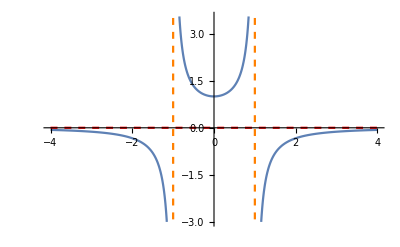

```mathematica
p1=Plot[1/(1-x^2),{x,-4,4},Exclusions->{-1,1}];
p2=ContourPlot[{x==-1,x==1},{x,-2,2},{y,-3,3.5},ContourStyle->{{Orange,Dashed},{Orange,Dashed}}];
p3=Plot[0,{x,-4,4},PlotStyle->{Red,Dashed}];
Show[p1,p2,p3]
```

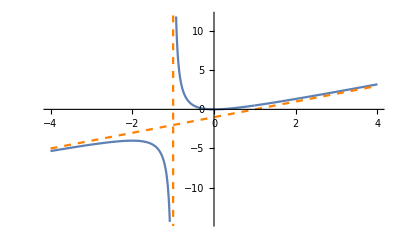

```mathematica
p1=Plot[x^2/(1+x),{x,-4,4},Exclusions->{-1,1}];
p2=ContourPlot[x==-1,{x,-2,2},{y,-15,12},ContourStyle->{Orange,Dashed}];
p3=Plot[x-1,{x,-4,4},PlotStyle->{Orange,Dashed}];
Show[p1,p2,p3]
```